```mathematica
F[ivv_,ivh_,ihv_,ihh_]:=(ivv/ihv-ivh/ihh)/(ivv/ihv+2ivh/ihh);
```

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ihh]]
```

(3 ihv ivh ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ivh]]
```

-(3 ihh ihv ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ihv]]
```

-(3 ihh ivh ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ivv]]
```

(3 ihh ihv ivh)/(2 ihv ivh+ihh ivv)^2

data/mini.ods

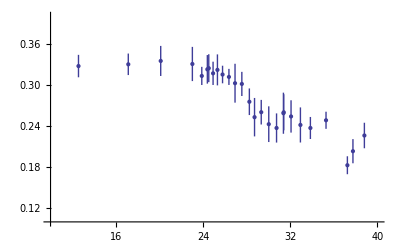

```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/mini.ods"])//TableForm
Needs["ErrorBarPlots`"]
Needs["ErrorBarPlots`"]
kotz2=First@Import[files[[1]]];
kotz2=kotz2[[2;;Length[kotz2]]];
ErrorListPlot[kotz2,PlotRange->{{10,40},{0.1,0.4}}]
```

```mathematica
kotzforfit=Join[kotz2[[1;;Length[kotz2]-3]],{kotz2[[Length[kotz2]]]}];
kotzfit={#[[1]],#[[2]]}&/@kotzforfit;
kotzerror=#[[3]]&/@kotzforfit;
kotzforfit//TableForm;
kotzfit//TableForm;
kotzerror//TableForm;
```

FittedModel[0.326308-0.00152749 x+0.0305 Erf[27.9381-x]]

FittedModel[0.32317-0.00144986 x+0.0300325 Erf[28.0454-x]]

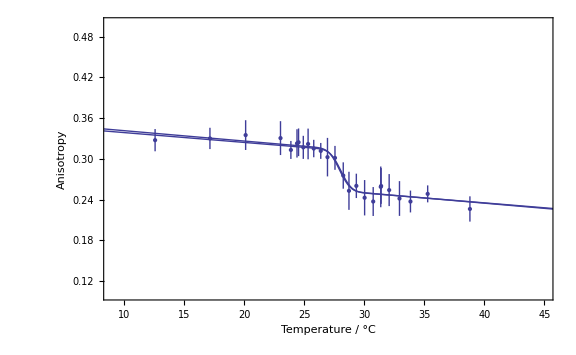

```mathematica
fit=NonlinearModelFit[kotzfit,h+a1*x+a2*Erf[x-xc],{a1,a2,h,{xc,26}},x]
fiter=NonlinearModelFit[kotzfit,h+a1*x+a2*Erf[x-xc],{a1,a2,h,{xc,26}},x,Weights->1/kotzerror^2]
Show[ErrorListPlot[kotzforfit,PlotRange->{{9,45},{0.1,0.5}}],Plot[Normal@fit,{x,0,50}],Plot[Normal@fiter,{x,0,50}],ImageSize->Large,Frame->True,FrameLabel->{"Temperature  / °C","Anisotropy"},Axes->None]
```

FittedModel[0.32317-0.00144986 x+0.0300325 Erf[28.0454-x]]

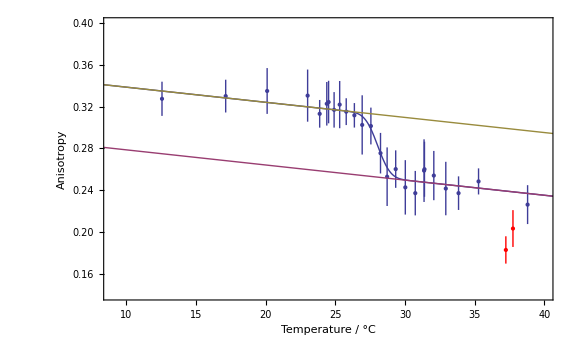

| Estimate | Standard Error | Confidence Interval
a1 | -0.00144986 | 0.00039227 | {-0.00226563,-0.000634095}
a2 | -0.0300325 | 0.00251382 | {-0.0352603,-0.0248048}
h | 0.32317 | 0.0111464 | {0.29999,0.346351}
xc | 28.0454 | 0.170224 | {27.6914,28.3994}

```mathematica
fit=NonlinearModelFit[kotzfit,h+a1*x+a2*Erf[x-xc],{a1,a2,h,{xc,26}},x,Weights->1/kotzerror^2]
Show[ErrorListPlot[kotzforfit,PlotRange->{{9,40},{0.14,0.4}},PlotRange->{{9,45},{0.15,0.4}}],ErrorListPlot[kotz2[[Length[kotz2]-2;;Length[kotz2]-1]],PlotStyle->Red],Plot[{Normal@fit,m1line,m2line},{x,0,50}],ImageSize->Large,Frame->True,FrameLabel->{"Temperature  / °C","Anisotropy"},Axes->None]
fit["ParameterConfidenceIntervalTable"]
```

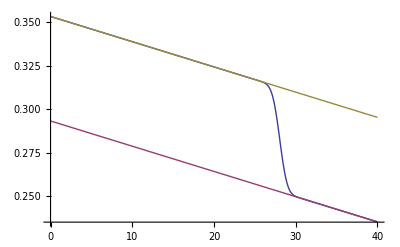

```mathematica
m2line=.;
m1line=.;
m2line[x_]:=(0.32317027145146426-0.0014498643188482188 x+0.030032532480167514);
m1line[x_]:=(0.32317027145146426-0.0014498643188482188 x-0.030032532480167514);
Plot[{Normal@fit,m1line[x],m2line[x]},{x,0,40}]
```

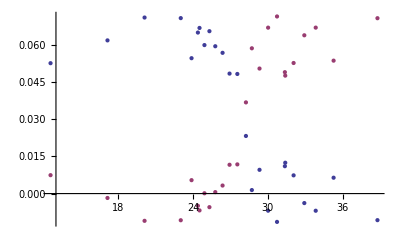

```mathematica
M1={#[[1]],#[[2]]-m1line[#[[1]]]}&/@kotzforfit;
M2={#[[1]],m2line[#[[1]]]-#[[2]]}&/@kotzforfit;
ListPlot[{M1,M2}]
T=.;
T=Table[{M1[[i,1]],M2[[i,2]]/(M1[[i,2]]+M2[[i,2]])},{i,1,Length[M1]}];
```

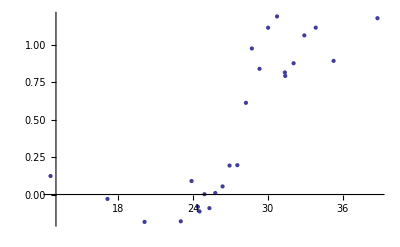

```mathematica
ListPlot[T]
```